## Oscillations and Waves Exam 3

## April 29, 2025

## This exam tests your fluency with the core of the Wolfram Language, as it was presented in An Elementary Introduction to the Wolfram Language, 3rd Edition (EIWL3), Sections 25-34 and 38-41. There is one problem with two or three parts corresponding to each section. Tip: all of them are meant to be quick. If you get bogged down, move on.

## Directions: After downloading this notebook, rename it with your first name in the filename. E.g., Eli-Exam3.nb, Harper-Exam3.nb, Hexi-Exam3.nb, Jeremy-Exam3.nb, Rania-Exam3.nb, Tahm-Exam3.nb, or Walker-Exam3.nb. Then disconnect from the wifi and work the exam. Save your notebook early and often so that you don’t lose work in progress. Your answers always go into the Wolfram Language Input cells that begin with a comment, e.g., (* 1a *) foobar /@ Plus[Array] All your answers should execute and re-execute without warnings or error messages. You may refer to your downloaded copies of EIWL3, and anything else we developed in the course (like your cheat sheets!), but not to any web resources. When you are done, save your notebook one last time, re-join the wifi, and then email it to me. This exam was designed to require about 45 minutes, but if you need a full hour, that is ok. Everyone will stop at the one-hour mark.

### 1. Applying Functions (EIWL3 Section 25)

#### (a)

Use Map with a levelspec to put a frame around each individual number in the array Array[Plus,{10,10}] (we don’t want frames around already-framed things — just one level of frames around the individual numbers).

```mathematica
(* 1a *) Framed/@Flatten[Array[Plus,{10,10}]]
```

{2,3,4,5,6,7,8,9,10,11,3,4,5,6,7,8,9,10,11,12,4,5,6,7,8,9,10,11,12,13,5,6,7,8,9,10,11,12,13,14,6,7,8,9,10,11,12,13,14,15,7,8,9,10,11,12,13,14,15,16,8,9,10,11,12,13,14,15,16,17,9,10,11,12,13,14,15,16,17,18,10,11,12,13,14,15,16,17,18,19,11,12,13,14,15,16,17,18,19,20}

#### (b)

Copy what you did in (a), but for this part, also turn the result into a grid using Grid and the “as an afterthought” syntax:

```mathematica
(* 1b *) Partition[Framed/@Flatten[Array[Plus,{10,10}]],10]//Grid
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

### 2. Pure Anonymous Functions (EIWL3 Section 26)

#### (a)

Use the # and & notation to create an anonymous function that cubes whatever is given it, and then use /@ to apply it to every member of the list {1,2,3,4,5}.

```mathematica
(* 2a *) #^3&/@Range[5]
```

{1,8,27,64,125}

#### (b)

Use the #1, #2, and & notation to create an anonymous function that divides its first argument by its second argument. Combine this with Apply and a levelspec to apply the function to {{1,2},{2,3},{3,4},{4,5}}. Once you have this right, you will get {1/2,2/3,3/4,4/5} .

```mathematica
(* 2b *)#1/#2&@@Transpose[{{1,2},{2,3},{3,4},{4,5}}]
```

{1/2,2/3,3/4,4/5}

```mathematica
Apply
```

### 3. Applying Functions Repeatedly (EIWL3 Section 27)

#### (a)

Use Nest to apply Factorial twice to {1,2,3,4}. If you have this right, 620,448,401,733,239,439,360,000 will be one of the elements of your answer.

```mathematica
(* 3a *) Nest[Factorial,{1,2,3,4},2]
```

{1,2,720,620448401733239439360000}

#### (b)

Use NestList to apply Factorial three times to {1,2,3}, as well as showing the results of doing it 0, 1, and 2 times. If you have this right, you will have an insanely large result at the third step. Do not go any higher, or I do not know what will happen to your computer.

```mathematica
(* 3b *) NestList[Factorial,{1,2,3},3]
```

{{1,2,3},{1,2,6},{1,2,720},{1,2,2601218943565795100204903227081043611191521875016945785727541837850835631156947382240678577958130457082619920575892247259536641565162052015873791984587740832529105244690388811884123764341191951045505346658616243271940197113909845536727278537099345629855586719369774070003700430783758997420676784016967207846280629229032107161669867260548988445514257193985499448939594496064045132362140265986193073249369770477606067680670176491669403034819961881455625195592566918830825514942947596537274845624628824234526597789737740896466553992435928786212515967483220976029505696699927284670563747137533019248313587076125412683415860129447566011455420749589952563543068288634631084965650682771552996256790845235702552186222358130016700834523443236821935793184701956510729781804354173890560727428048583995919729021726612291298420516067579036232337699453964191475175567557695392233803056825308599977441675784352815913461340394604901269542028838347101363733824484506660093348484440711931292537694657354337375724772230181534032647177531984537341478674327048457983786618703257405938924215709695994630557521063203263493209220738320923356309923267504401701760572026010829288042335606643089888710297380797578013056049576342838683057190662205291174822510536697756603029574043387983471518552602805333866357139101046336419769097397432285994219837046979109956303389604675889865795711176566670039156748153115943980043625399399731203066490601325311304719028898491856203766669164468791125249193754425845895000311561682974304641142538074897281723375955380661719801404677935614793635266265683339509760000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}

### 4. Tests and Conditionals (EIWL3 Section 28)

#### (a)

Use PrimeQ and /@ to generate a True or False list that is twenty elements long expressing which numbers in Range[20] are prime.

```mathematica
(* 4a *) PrimeQ/@Range[20]
```

{False,True,True,False,True,False,True,False,False,False,True,False,True,False,False,False,True,False,True,False}

#### (b)

Combine PrimeQ with Select to only list the numbers in Range[20] that are prime.

```mathematica
(* 4b *) Select[Range[20],PrimeQ]
```

{2,3,5,7,11,13,17,19}

### 5. More About Pure Functions (EIWL3 Section 29)

#### (a)

Accomplish exactly the same thing as Table[n*(n-1)/2,{n,6}] using Array and a pure function.

```mathematica
(* 5a *) Array[#*(#-1)&,6]
```

{0,2,6,12,20,30}

#### (b)

Make some modifications to FoldList[Plus,{1,2,3,4,5}] so that it produces a list of the first 10 factorials. Instead of hand-coding the list up to 10, begin by first changing {1,2,3,4,5} to Range[10].

```mathematica
(* 5b *) FoldList[Times,Range[10]]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

### 6. Rearranging Lists (EIWL3 Section 30)

#### (a)

Use Transpose and one of the levelspec options to turn {{{1,uno},{2,dos},{3,tres}},{{4,cuatro},{5,cinco},{6,seis}}} into {{{1,2,3},{uno,dos,tres}},{{4,5,6},{cuatro,cinco,seis}}}

```mathematica
(* 6a *) Flatten/@{{{1,uno},{2,dos},{3,tres}},{{4,cuatro},{5,cinco},{6,seis}}} (*NW*)
```

{{1,uno,2,dos,3,tres},{4,cuatro,5,cinco,6,seis}}

#### (b)

Use Flatten and a levelspec option to turn {{{1,uno},{2,dos},{3,tres}},{{4,cuatro},{5,cinco},{6,seis}}} into {{1,uno},{2,dos},{3,tres},{4,cuatro},{5,cinco},{6,seis}}

```mathematica
(* 6b *)Partition[Flatten[{{{1,uno},{2,dos},{3,tres}},{{4,cuatro},{5,cinco},{6,seis}}}],2]
```

{{1,uno},{2,dos},{3,tres},{4,cuatro},{5,cinco},{6,seis}}

### 7. Parts of Lists (EIWL3 Section 31)

#### (a)

Use the magical All position (you will need to use All more than once) to turn {{{Eli, Lerner},{Harper,Yonago},{Hexi,Jin}},{{Jeremy,Choy},{Rania,Zaki},{Tahm,Loyd},{Walker,Harris}}} into {{Eli,Harper,Hexi},{Jeremy,Rania,Tahm,Walker}}

```mathematica
(* 7a *) {{{Eli, Lerner},{Harper,Yonago},{Hexi,Jin}},{{Jeremy,Choy},{Rania,Zaki},{Tahm,Loyd},{Walker,Harris}}}[[All,All,1]]
```

{{Eli,Harper,Hexi},{Jeremy,Rania,Tahm,Walker}}

#### (b)

Use a magical negative positional argument to extract {Jeremy,Rania,Tahm,Walker} from  {{Eli,Harper,Hexi},{Jeremy,Rania,Tahm,Walker}} and combine that with Take with a different magical negative argument to extract {Tahm,Walker}.

```mathematica
(* 7b *) Take[{{Eli,Harper,Hexi},{Jeremy,Rania,Tahm,Walker}}[[-1]],-2]
```

{Tahm,Walker}

### 8. Patterns (EIWL3 Section 32)

#### (a)

Use Cases to choose the lists that begin and end with the same letter in this list of lists (but look ahead to part (b) before you solve part (a)): 

{
 {“a”, “l”, “u”, “l”, “a”}, 
 {“a”, “l”, “o”, “h”, “a”},
 {“a”, “r”, “a”, “r”, “a”}, 
 {“b”, “o”, “n”, “u”, “s”},
 {“c”, “i”, “v”, “i”, “c”},
 {“d”, “e”, “b”, “e”, “d”}, 
 {“e”, “l”, “b”, “o”, “w”},
 {“z”, “a”},
 {“z”, “z”}
}

```mathematica
(* 8a *) Cases[{{"a", "l", "u", "l", "a"}, 
 {"a", "l", "o", "h", "a"},
 {"a", "r", "a", "r", "a"}, 
 {"b", "o", "n", "u", "s"},
 {"c", "i", "v", "i", "c"},
 {"d", "e", "b", "e", "d"}, 
 {"e", "l", "b", "o", "w"},
 {"z", "a"},
 {"z", "z"}},{x_,__,x_}]
```

{{a,l,u,l,a},{a,l,o,h,a},{a,r,a,r,a},{c,i,v,i,c},{d,e,b,e,d}}

#### (b)

The pattern  BlankNullSequence has the shorthand ___. Use ___ to improve the pattern you used in Part (a) so that the two-letter list {z,z} is also included in your result.

```mathematica
(* 8b *) Cases[{{"a", "l", "u", "l", "a"}, 
 {"a", "l", "o", "h", "a"},
 {"a", "r", "a", "r", "a"}, 
 {"b", "o", "n", "u", "s"},
 {"c", "i", "v", "i", "c"},
 {"d", "e", "b", "e", "d"}, 
 {"e", "l", "b", "o", "w"},
 {"z", "a"},
 {"z", "z"}},{x_,___,x_}]
```

{{a,l,u,l,a},{a,l,o,h,a},{a,r,a,r,a},{c,i,v,i,c},{d,e,b,e,d},{z,z}}

### 9. Assigning Names to Things (EIWL3 Section 38)

#### (a)

Use Module to compute x=Factorial[10], and then produce {x,x^2,x^3}.

```mathematica
(* 9a *) Module[{x=Factorial[10]},{x,x^2,x^3}]
```

{3628800,13168189440000,47784725839872000000}

#### (b)

Inside Module, let rangeSquared=Range[10]^2, and then produce a list line plot of rangeSquared joined with Reverse[rangeSquared].

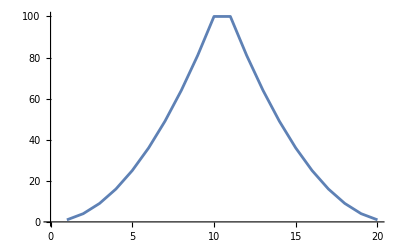

```mathematica
(* 9b *) Module[{rangeSquared=Range[10]^2},ListLinePlot[Join[rangeSquared,Reverse[rangeSquared]]]]
```

### 10. Immediate and Delayed Values (EIWL3 Section 39)

#### (a)

Make a one-character change to this expression, Module[{x:=RandomInteger[10]},{x,x^2,x^3,x^4}], so that it produces four different powers of the same random number instead of four different powers of different random numbers.

```mathematica
(* 10a *) Module[{x=RandomInteger[10]},{x,x^2,x^3,x^4}]
```

{6,36,216,1296}

#### (b)

Make a one-character change to this expression, Module[{color=RandomColor[]},Graphics[Table[Style[Disk[{i,0}],color],{i,5}]]], so that it produces five different-color disks.

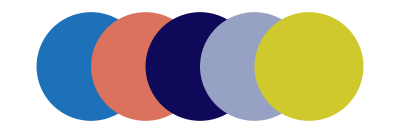

```mathematica
(* 10b *) Module[{color:=RandomColor[]},Graphics[Table[Style[Disk[{i,0}],color],{i,5}]]]
```

### 11. Defining Your Own Functions (EIWL3 Section 40)

#### (a)

Define a function f that takes a list of three elements and out of them makes a list of lists that contains all six possible orderings. Using Permutations will make this easy.

Include a test of your function as f[1,2,3] and make sure it gets {{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}.

```mathematica
(* 11a *) f[x_,y_,z_]:=Permutations[{x,y,z}]
```

```mathematica
f[1,2,3]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

#### (b)

Define a function g that gives 1 for g[0], and gives n*g[n-1] for any integer n greater than 0, but don’t use an If statement! Include a test of your function as g[6] and make sure it gets 720.

```mathematica
(* 11b *)g[x_]:=1/;x==0
g[x_]:=x*(g[x-1])/;x>0
g[5] (*for some reason, I am reaching my recursion limit at 5*)
```

120

### 12. More About Patterns (EIWL3 Section 41)

#### (a)

Use the replacement rule notation — e.g., /. and -> — to exchange the first and last element in any list containing two or more elements and test your replacement using the list {alpha, beta, gamma, delta, epsilon}.

```mathematica
(* 12a *) listFunction[l_List]:= l /. First[l]->Last[l]& Last[l]->First[l]
```

```mathematica
listFunction[{alpha, beta, gamma, delta, epsilon}]
```

epsilon ({alpha,beta,gamma,delta,epsilon}/.First[{alpha,beta,gamma,delta,epsilon}]→Last[{alpha,beta,gamma,delta,epsilon}]&)→alpha

#### (b)

Starting with Characters/@RomanNumeral[Range[100], select all the sequences corresponding to the Roman numerals that have XXX in them.

```mathematica
(* 12b *) Cases[Characters/@RomanNumeral[Range[100]],{___,"X","X","X",___}]
```

{{X,X,X},{X,X,X,I},{X,X,X,I,I},{X,X,X,I,I,I},{X,X,X,I,V},{X,X,X,V},{X,X,X,V,I},{X,X,X,V,I,I},{X,X,X,V,I,I,I},{X,X,X,I,X},{L,X,X,X},{L,X,X,X,I},{L,X,X,X,I,I},{L,X,X,X,I,I,I},{L,X,X,X,I,V},{L,X,X,X,V},{L,X,X,X,V,I},{L,X,X,X,V,I,I},{L,X,X,X,V,I,I,I},{L,X,X,X,I,X}}

#### (c)

Use StringJoin to turn what you got in 12(b) into {XXX,XXXI,XXXII,XXXIII,XXXIV,XXXV,XXXVI,XXXVII,XXXVIII,XXXIX,LXXX,LXXXI,LXXXII,LXXXIII,LXXXIV,LXXXV,LXXXVI,LXXXVII,LXXXVIII,LXXXIX}.

```mathematica
(* 12c *) StringJoin/@Cases[Characters/@RomanNumeral[Range[100]],{___,"X","X","X",___}]
```

{XXX,XXXI,XXXII,XXXIII,XXXIV,XXXV,XXXVI,XXXVII,XXXVIII,XXXIX,LXXX,LXXXI,LXXXII,LXXXIII,LXXXIV,LXXXV,LXXXVI,LXXXVII,LXXXVIII,LXXXIX}

```mathematica
Replace
```